```mathematica
DSolve[y''[x]-y'[x]-6y[x]== 0, y[x], x]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^(3 x) C[2]}}

```mathematica
p1=Exp[-2x]
p2 = Exp[3x]
Plot[ {p1,p2},{x, 0, 1}, PlotLabels-> {"exp(-2x)", "exp(3x)"}, PlotStyle-> {Thickness[0.012], Thickness[0.012]}]
```

ⅇ^(-2 x)

ⅇ^(3 x)

-Graphics-

```mathematica
sol = y''[x] + 9y[x] == 0
sol1 = DSolve[sol, y[x], x]
```

9 y[x]+y''[x]==0

{{y[x]→C[1] Cos[3 x]+C[2] Sin[3 x]}}

Cos[3 x]

Sin[3 x]

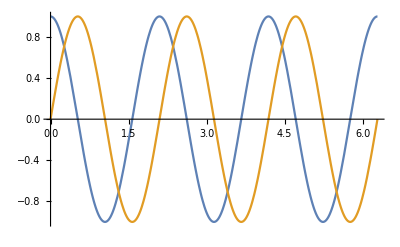

```mathematica
p3 = Cos[3x]
p4 = Sin[3x]
Plot[{p3, p4},{x, 0, 2Pi}]
```

```mathematica
eqn = T''[t] == U(T[t]-A)
DSolve[eqn, T[t], t]
```

```mathematica
Plot[{Exp[t]+Exp[-t]},{t,0,1}]
```

```mathematica
sol = y''[x]-10y'[x]+25y[x] == 30x + 3
DSolve[sol,y[x],x]
sol1 = 0.6(1+2x)+Exp[5x]+x*Exp[5x]
∫_0^x (x-s)Exp[5(x-s)]*(30s+3)ⅆs
Plot[sol1,{x,-4,1}, PlotRange->{-3,3}, PlotLabel->"0.6(1+2x)+Exp[5x]+x*Exp[5x]", PlotStyle-> Thickness[0.012]]
```

```mathematica
sol2 = y''[x]-8y'[x]+20y[x]== 100x^2-26x*Exp[x]
sol3 = DSolve[sol2,y[x],x]
```

```mathematica
{{y[x]->ⅇ^(4 x) C[2] Cos[2 x]+ⅇ^(4 x) C[1] Sin[2 x]-1/130 (-143+120 ⅇ^x-520 x+260 ⅇ^x x-650 x^2) (Cos[2 x]^2+Sin[2 x]^2)}}
Plot[y== Cos[x]^2+Sin[x]^2,{x,0,1}]
```

```mathematica
1/2∫_0^x Exp[4(x-s)]*Sin[2(x-s)]*(100s^2-26s*Exp[s])ⅆs
```

```mathematica
1/2 (11/5-(24 ⅇ^x)/13+8 x-4 ⅇ^x x+10 x^2-23/65 ⅇ^(4 x) Cos[2 x]-24/65 ⅇ^(4 x) Sin[2 x])
```

False

```mathematica
1/8∫_0^x 2*Exp[4s]*(Exp[4(x-s)]-Exp[-4(x-s)])ⅆs
```

1/8 (2 ⅇ^(4 x) x-1/2 Sinh[4 x])

```mathematica
Evaluate[2 ⅇ^(4 x) x-1/2 Sinh[4 x]]
```

2 ⅇ^(4 x) x-1/2 Sinh[4 x]

```mathematica
1/2 (-1+ⅇ^(4 x))^2=== 1/8(2*Exp[4x]*x-1/4(Exp[4x]-Exp[-4x]))
```

False

-16 y[x]+y''[x]==2 ⅇ^(4 x)

{{y[x]→1/32 ⅇ^(4 x) (-1+8 x)+ⅇ^(4 x) C[1]+ⅇ^(-4 x) C[2]}}

ⅇ^(-4 x)+ⅇ^(4 x)+1/32 ⅇ^(4 x) (-1+8 x)

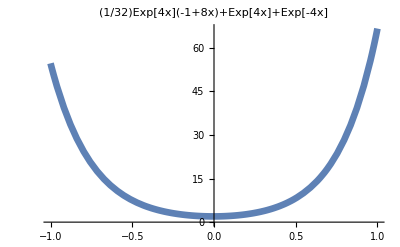

```mathematica
sol4 = y''[x]-16y[x]== 2Exp[4x]
DSolve[sol4, y[x],x]
sol5 = (1/32)Exp[4x](-1+8x)+Exp[4x]+Exp[-4x]
Plot[sol5, {x,-1,1},PlotStyle->Thickness[0.012],PlotLabel->"(1/32)Exp[4x](-1+8x)+Exp[4x]+Exp[-4x]"]
```

```mathematica
∫_0^x Sin[x-s]2s*Sin[s]ⅆs
sol8 = y''[x]+y[x] == 2x*Sin[x]
DSolve[sol8, y[x],x]


∫_0^x (Exp[x-s]*Sin[x-s](Exp[2s]*(Cos[s]-3Sin[s])))ⅆs
sol7 =y''[x]-2y'[x]+2y[x]==Exp[2x]*(Cos[x]-3Sin[x])
DSolve[sol7, y[x],x]
```

-1/2 x (x Cos[x]-Sin[x])

y[x]+y''[x]==2 x Sin[x]

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/4 (-2 x^2 Cos[x]+Cos[x] Cos[2 x]-2 x Cos[2 x] Sin[x]+2 x Cos[x] Sin[2 x]+Sin[x] Sin[2 x])}}

```mathematica
Simplify[1/5 ⅇ^x (7 (-1+ⅇ^x) Cos[x]-(6+ⅇ^x) Sin[x])]
```

1/5 ⅇ^x (7 (-1+ⅇ^x) Cos[x]-(6+ⅇ^x) Sin[x])

```mathematica
{{y[x]->ⅇ^x C[2] Cos[x]+ⅇ^x C[1] Sin[x]+1/10 ⅇ^(2 x) (15 Cos[x]-Cos[x] Cos[2 x]+5 Sin[x]+7 Cos[2 x] Sin[x]-7 Cos[x] Sin[2 x]-Sin[x] Sin[2 x])}}
```

1/8 (2 ⅇ^(4 x) x-1/2 Sinh[4 x])

-16 y[x]+y''[x]==2 ⅇ^(4 x)

{{y[x]→1/32 ⅇ^(4 x) (-1+8 x)+ⅇ^(4 x) C[1]+ⅇ^(-4 x) C[2]}}

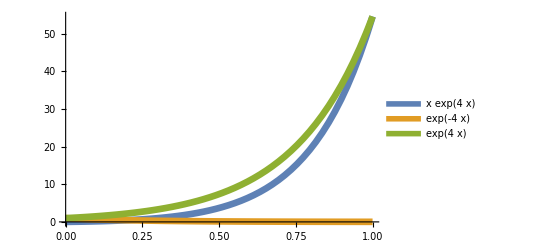

```mathematica
1/8∫_0^x 2*Exp[4s](Exp[4(x-s)]-Exp[-4(x-s)])ⅆs
sol9 = y''[x]-16y[x]== 2*Exp[4x]
DSolve[sol9, y[x],x]
Plot[{x*Exp[4x], Exp[-4x], Exp[4x]},{x, 0,1}, PlotStyle->{Thickness[0.012],Thickness[0.012],Thickness[0.012]}, PlotLegends->"Expressions"]
```

```mathematica
∫_0^x Sin[x-s]*2s*Sin[s]ⅆs
```

-1/2 x (x Cos[x]-Sin[x])

```mathematica
-∫_0^x Sin[2(x-s)]ⅆs
```

-Sin[x]^2

```mathematica
Log[Exp[4]]
```

4

```mathematica
∫_0^t (t-s)*Exp[-t]*Log[s]ⅆs
```

```mathematica
1/4 ⅇ^-t t^2 (-3+2 Log[t])

sol11 = y''[t]+2y'[t]+y[t]== Exp[-t]*Log[t]
DSolve[sol11, y[t],t]
```

1/4 ⅇ^-t t^2 (-3+2 Log[t])

y[t]+2 y'[t]+y''[t]==ⅇ^-t Log[t]

```mathematica
{{y[t]->ⅇ^-t C[1]+ⅇ^-t t C[2]+1/4 ⅇ^-t t^2 (-3+2 Log[t])}}

1/6∫_0^t (Exp[2(t-s)]-Exp[-6(t-s)])(2*Exp[-2s]-Exp[-s])ⅆs
```

{{y[t]→ⅇ^-t C[1]+ⅇ^-t t C[2]+1/4 ⅇ^-t t^2 (-3+2 Log[t])}}

```mathematica
1/180 ⅇ^(-6 t) (9-30 ⅇ^(4 t)+16 ⅇ^(5 t)+5 ⅇ^(8 t))

∫_0^t Sin(i(t-s))ⅆs
```

1/180 ⅇ^(-6 t) (9-30 ⅇ^(4 t)+16 ⅇ^(5 t)+5 ⅇ^(8 t))

```mathematica
1/2 i Sin t^2

Plot[Exp[-x] + Exp[x],{x,0,1}]
```

1/2 i Sin t^2

0.49751 (1.10517 ⅇ^(-0.1 x)+0.904837 ⅇ^(0.1 x))

(ⅇ^(10-10 x)+ⅇ^(-10+10 x))/(1/ⅇ^10+ⅇ^10)

(ⅇ^(1-x)+ⅇ^(-1+x))/(1/ⅇ+ⅇ)

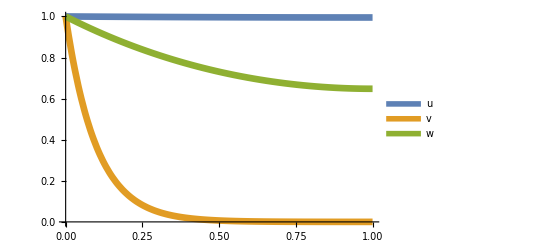

```mathematica
u = ((Exp[-0.1]*Exp[0.1x])+(Exp[0.1]*Exp[-0.1x]))/(Exp[-0.1]+Exp[0.1])
v = ((Exp[-10]*Exp[10x])+(Exp[10]*Exp[-10x]))/(Exp[-10]+Exp[10])
w = ((Exp[-1]*Exp[x])+(Exp[1]*Exp[-x]))/(Exp[-1]+Exp[1])
Plot[{u,v, w},{x,0,1}, PlotStyle->{Thickness[0.012],Thickness[0.012],Thickness[0.012]}, PlotLegends-> "Expressions"]

1/L∫_0^L uⅆx
```

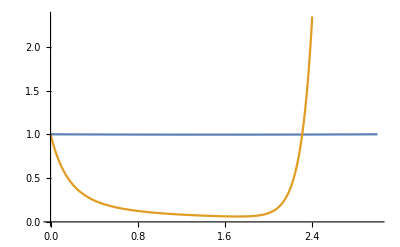

```mathematica
Plot[{(0.996679946249559-5.49833997312478 ⅇ^(-0.1 L)+4.501660026875221 ⅇ^(0.1 L))/L, 1/L∫_0^L vⅆx},{L,0,3}]
```

```mathematica
mat = {{1,5,3},{4,9,6},{7,19,9}}
mat//MatrixForm
mat1 = {{x},{y},{z}}
mat//MatrixForm
mat2 = {{1},{5},{9}}
mat//MatrixForm
Solve[mat.mat1 == mat2]
```

{{1,5,3},{4,9,6},{7,19,9}}

(1 | 5 | 3
4 | 9 | 6
7 | 19 | 9)

{{x},{y},{z}}

(1 | 5 | 3
4 | 9 | 6
7 | 19 | 9)

{{1},{5},{9}}

(1 | 5 | 3
4 | 9 | 6
7 | 19 | 9)

{{x→3/2,y→0,z→-1/6}}

```mathematica
{{x->3/2,y->0,z->-1/6}}

Limit[Sin[x]/x,x-> 0]
```

{{x→3/2,y→0,z→-1/6}}

1

```mathematica
Solve[x^2+8x+20 == 0,x]  

DSolve[{n''[x]+2x*n'[x]== 0, n[0]== 1, n[∞]== 0},n[x],x]
```

{{x→-4-2 ⅈ},{x→-4+2 ⅈ}}

{{n[x]→1-Erf[x]}}

```mathematica
{{x->-4-2 ⅈ},{x->-4+2 ⅈ}}
```

```mathematica
n[x/(2*Sqrt[1])_]== 1-Erf[x/(2*Sqrt[1])]
Plot[{1-Erf[x/(2*Sqrt[1])],1-Erf[x/(2*Sqrt[10])],1-Erf[x/(2*Sqrt[100])]},{x,0,3}]
```

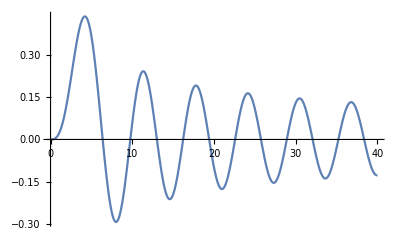

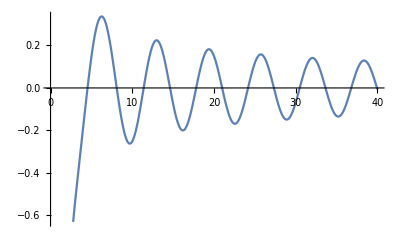

```mathematica
Plot[BesselJ[3,x],{x,0,40}]
Plot[BesselY[3,x],{x,0,40}]
```

```mathematica
Solve[{{1/600.0,1/500.0},{1,1}}.{{u},{v}}== {{1200/700},{1000}}]
```

```mathematica
{{u->857.1428571428577,v->142.85714285714226}}

mat16
```

```mathematica
DSolve[{k*x''[t]== 0, },x[t],t]
```

{{x[t]→C[1]+t C[2]}}

```mathematica
pde = D[T[x,t], t]=k*(∂_t)^2 T[x,t]
DSolve[pde,T[x,t],{x,t}]
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Eigenvectors[{{0,1},{1,-2h}}]
Eigenvalues[{{0,1},{1,-2h}}]
Norm[{{0,1},{1,-h}},1]
Norm[{{0,1},{1,-h}},2]
```

{{h-√(1+h^2),1},{h+√(1+h^2),1}}

{-h-√(1+h^2),-h+√(1+h^2)}

Max[1,1+Abs[h]]

Max[(√(2+h Conjugate[h]-√h √Conjugate[h] √(4+h Conjugate[h])))/(√2),(√(2+h Conjugate[h]+√h √Conjugate[h] √(4+h Conjugate[h])))/(√2)]

```mathematica
Inverse[{{-Subscript[λ, 1],-Subscript[λ, 2]},{1,1}}]
Inverse[{{1,1},{Subscript[λ, 1],Subscript[λ, 2]}}]
```

```mathematica
{{1/(-Subscript[λ, 1]+Subscript[λ, 2]),Subscript[λ, 2]/(-Subscript[λ, 1]+Subscript[λ, 2])},{-1/(-Subscript[λ, 1]+Subscript[λ, 2]),-Subscript[λ, 1]/(-Subscript[λ, 1]+Subscript[λ, 2])}}
```

```mathematica
{{Subscript[λ, 2]/(-Subscript[λ, 1]+Subscript[λ, 2]),-1/(-Subscript[λ, 1]+Subscript[λ, 2])},{-Subscript[λ, 1]/(-Subscript[λ, 1]+Subscript[λ, 2]),1/(-Subscript[λ, 1]+Subscript[λ, 2])}}
```

```mathematica
Max[(√(2+h Conjugate[h]-√h √Conjugate[h] √(4+h Conjugate[h])))/(√2),(√(2+h Conjugate[h]+√h √Conjugate[h] √(4+h Conjugate[h])))/(√2)]

-h-Sqrt[1+h^2]== -1
```

Max[(√(2+h Conjugate[h]-√h √Conjugate[h] √(4+h Conjugate[h])))/(√2),(√(2+h Conjugate[h]+√h √Conjugate[h] √(4+h Conjugate[h])))/(√2)]

```mathematica
{{-Subscript[λ, 1],-Subscript[λ, 2]},{1,1}}.{{Subscript[λ, 1]^k,0},{0,Subscript[λ, 2]^k}}.{{1/(-Subscript[λ, 1]+Subscript[λ, 2]),Subscript[λ, 2]/(-Subscript[λ, 1]+Subscript[λ, 2])},{-1/(-Subscript[λ, 1]+Subscript[λ, 2]),-Subscript[λ, 1]/(-Subscript[λ, 1]+Subscript[λ, 2])}}
```

{{-λ_1^(1+k)/(-λ_1+λ_2)+λ_2^(1+k)/(-λ_1+λ_2),-(λ_1^(1+k) λ_2)/(-λ_1+λ_2)+(λ_1 λ_2^(1+k))/(-λ_1+λ_2)},{λ_1^k/(-λ_1+λ_2)-λ_2^k/(-λ_1+λ_2),(λ_1^k λ_2)/(-λ_1+λ_2)-(λ_1 λ_2^k)/(-λ_1+λ_2)}}

```mathematica
Lim[{{-(Subscript[λ, 1]^(1+k)/(-Subscript[λ, 1]+Subscript[λ, 2]))+Subscript[λ, 2]^(1+k)/(-Subscript[λ, 1]+Subscript[λ, 2]),-((Subscript[λ, 1]^(1+k) Subscript[λ, 2])/(-Subscript[λ, 1]+Subscript[λ, 2]))+(Subscript[λ, 1] Subscript[λ, 2]^(1+k))/(-Subscript[λ, 1]+Subscript[λ, 2])},{Subscript[λ, 1]^k/(-Subscript[λ, 1]+Subscript[λ, 2])-Subscript[λ, 2]^k/(-Subscript[λ, 1]+Subscript[λ, 2]),(Subscript[λ, 1]^k Subscript[λ, 2])/(-Subscript[λ, 1]+Subscript[λ, 2])-(Subscript[λ, 1] Subscript[λ, 2]^k)/(-Subscript[λ, 1]+Subscript[λ, 2])}},k-> ∞]
```

Lim[{{-(λ_1^(1+k)/(-λ_1+λ_2))+λ_2^(1+k)/(-λ_1+λ_2),-((λ_1^(1+k) λ_2)/(-λ_1+λ_2))+(λ_1 λ_2^(1+k))/(-λ_1+λ_2)},{λ_1^k/(-λ_1+λ_2)-λ_2^k/(-λ_1+λ_2),(λ_1^k λ_2)/(-λ_1+λ_2)-(λ_1 λ_2^k)/(-λ_1+λ_2)}},k→∞]

```mathematica
Norm[{{0,1},{1,-4}},1]
```

5

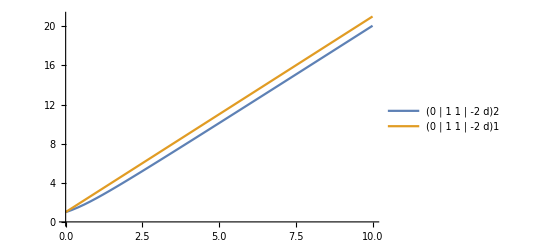

```mathematica
Plot[{Norm[{{0,1},{1,-2d}},2],Norm[{{0,1},{1,-2d}},1]},{d,0,10}, PlotLegends->"Expressions"]
```

ⅇ^(-x/1000)/1000

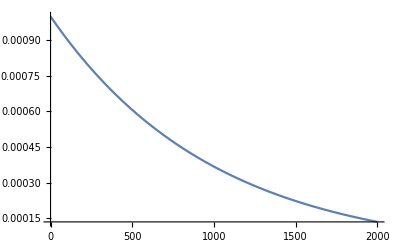

0.0497871

```mathematica
prob = Exp[-x/1000]/1000
Plot[prob, {x,0,2000}]
1.0*∫_3000^∞ probⅆx
```